```mathematica
nGrid = 10+1; Δy=1/(nGrid-1);
y = Table[(i-1)Δy,{i,1,nGrid}];
u=Array["u",nGrid];
```

```mathematica
discreteEqns = Table[u[[i+1]]-2u[[i]]+u[[i-1]]==0,{i,2,nGrid-1}];
```

```mathematica
bcs = {u[[1]]==0, u[[nGrid]]==10}
```

{u[1]==0,u[11]==10}

```mathematica
eqns = Join[discreteEqns,bcs];
```

```mathematica
sol = NSolve[eqns,u];
```

```mathematica
uVals=u/.sol;
```

```mathematica
data=Table[{y[[i]],uVals[[1]][[i]]},{i,nGrid}];
```

{{0,0.},{1/10,1.},{1/5,2.},{3/10,3.},{2/5,4.},{1/2,5.},{3/5,6.},{7/10,7.},{4/5,8.},{9/10,9.},{1,10.}}

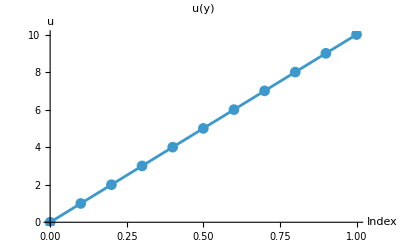

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,AxesLabel->{"Index","u"},PlotLabel->"u(y)"]
```